```mathematica
Rectan[r_,x_]:=Module[{dots={},AsR=r, Len=x,i,j,r1c,n,Dx,Dy,R2,center},
For[i=0,i<Len,i++,
For[j=0,j<Len*AsR,j++,

AppendTo[dots,{i,j}];
];];
center=Total[dots]/Length[dots];
r1c=Map[(#-center)&,dots];
n=Length[r1c];
Dx=Total[r1c[[All,1]]^2]/n;
Dy=Total[r1c[[All,2]]^2]/n;
R2=Total[r1c[[All,1]]^2+r1c[[All,2]]^2]/n;
Print["s1 = ",N[Dx/R2]];
Print["s2 = ",N[Dy/R2]];
Print["Asph = ",N[(Dx-Dy)^2/(Dx+Dy)^2]];
Return[N[(Dx-Dy)^2/(Dx+Dy)^2]];]
```

```mathematica
r1=Rectan[0.5,150];
```

s1 = 0.800021

s2 = 0.199979

Asph = 0.360051

```mathematica
r1
```

0.360051

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
data=Import["https://raw.githubusercontent.com/kamilla0503/saw/master/Ising/Geometry_Results/Geometry_Ising.txt", "Table"];
```

```mathematica
Union[data[[All,1]]]
```

{1000,2500,3600,4900}

```mathematica
dataNew={};
Do[

data0=Map[{{#[[2]],#[[3]]},ErrorBar[#[[4]]]}&,Select[data[[All,{1,2,12,13}]],#[[1]]==L&]];
AppendTo[dataNew,data0];
,{L,Union[data[[All,1]]]}];
```

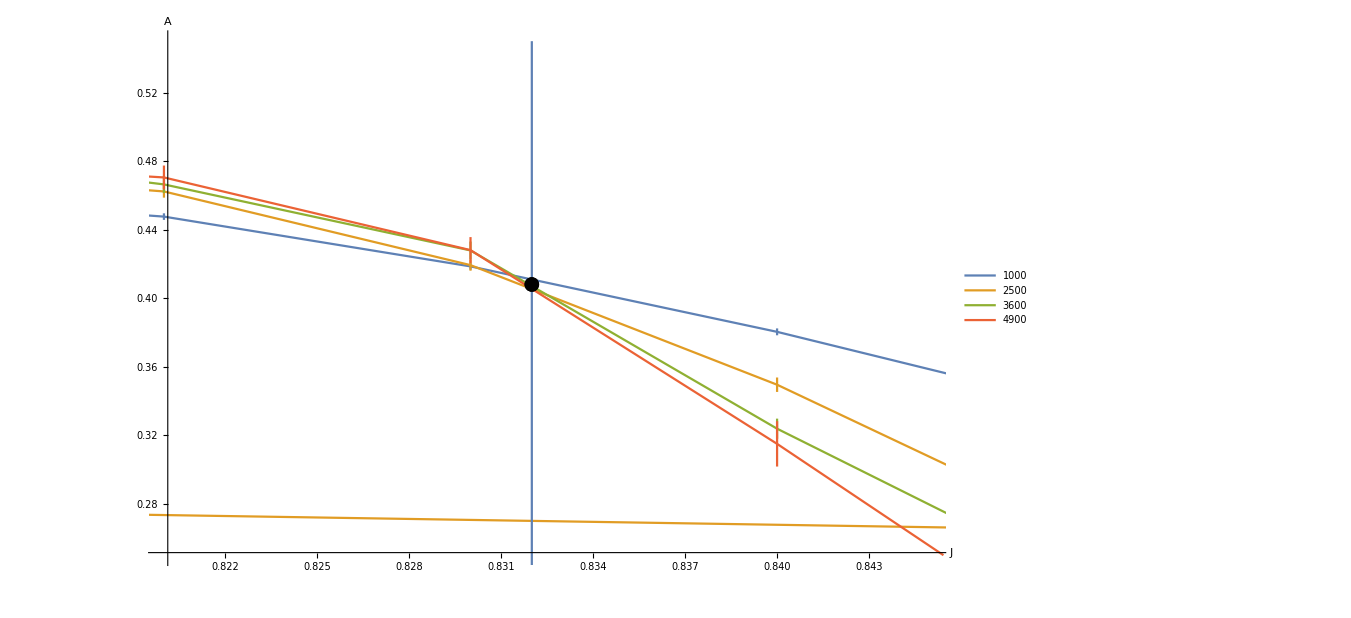

```mathematica
plt1=ErrorListPlot[dataNew, Joined->True,AxesLabel->{"J","A"},PlotRange->{{0.82,0.845},{0.25,0.55}},PlotLegends->Union[data[[All,1]]],ImageSize->1000];
plt2=ListPlot[{{0.832,0.15},{0.832,0.55}}, Joined->True];
plt3=ListPlot[{{0.832,0.408}},PlotMarkers->Style[•,Black,15]];
Show[plt1,plt2,plt3]
```

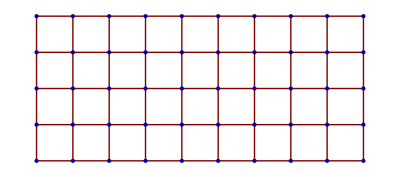

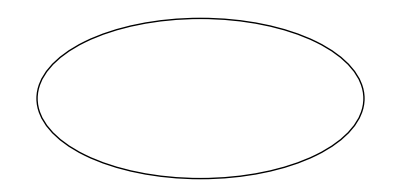

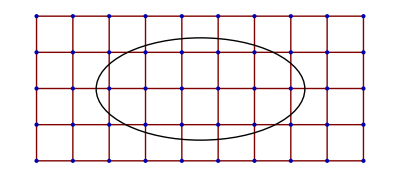
-Graphics-L r x L

```mathematica
a=GraphPlot[GridGraph[{5,10}], PlotStyle->PointSize[Large],PlotRangePadding->None]
b=Graphics[{Thick,Circle[{5.5,3},{2.87228,1.414}]}]
a=Labeled[Show[a,b],{Style["L ",20],Style["r x L",20]},{Bottom,Left},RotateLabel->True]
```

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
Export["RectanGrid.png",a];
```

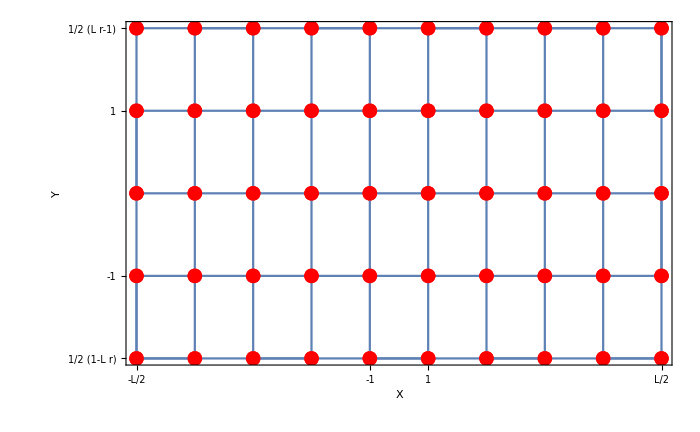

```mathematica
Data=Join[Array[{-5.5+#,2}&,10],Array[{5.5-#,1}&,10],Array[{#-5.5,0}&,10],Array[{5.5-#,-1}&,10],Array[{#-5.5,-2}&,10]];
a=ListPlot[Data,Joined->True,PlotMarkers->Style[•,Red,15]];
Data2=Join[Array[{4.5,3-#}&,5],Array[{3.5,#-3}&,5],Array[{2.5,3-#}&,5],Array[{1.5,#-3}&,5],Array[{0.5,3-#}&,5],Array[{-0.5,#-3}&,5],Array[{-1.5,3-#}&,5],Array[{-2.5,#-3}&,5],Array[{-3.5,3-#}&,5],Array[{-4.5,#-3}&,5]];
b=ListPlot[Data2,Joined->True,PlotMarkers->Style[•,Red,15]];
a=Show[a,b,Frame->{True,True,False,False},FrameTicks->{{{-4.5,-L/2,0.01},{4.5,L/2,0.01},{0.5,1,0.01},{-0.5,-1,0.01}},{{-2,-(r*L-1)/2,0.01},{2,(r*L-1)/2,0.01},{1,1,0.01},{-1,-1,0.01}}},FrameTicksStyle->Directive["Label", 17],ImageSize->700,AxesLabel->{Style[X,18],Style[Y,18]},AxesStyle->Thick]
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
Export["RectanGrid2.png",a];
```